## Evaporated the fur because it covers them

### Preface

Center of mass energy in collision s^(1/2) = 1.96 Tev. Absolute momentum 0 < p_max<s^(1/2)/2.

```mathematica
y=1;
m=1;
SetDirectory["/home/moosmann/mathematica/montecarlo"]
(*m=105.658369 10^6 ;  muon mass*)
```

SetDirectory::cdir: Cannot set current directory to "/home/moosmann/mathematica/montecarlo".

$Failed

SU(2)-Yang-Mills scale λ given by λ = y mu, where y parameterizes the uncertainty in the relation between λ and mu. Choose y = 1/2.
Hagedorn temperature T_H is given by T_H= 11.24/(2π) y mu. Assume further T ≈T_H

### Di-fermion spectrum

Di- and Multi- muon vertices are reconstructed for angles θ≤ 36 °, Cos[θ] ≥ cosmin:

```mathematica
cosmin:=0;
```

Full differential (w.r.t. x, θ and ϕ) fermion number density per unit time and surface :

```mathematica
Remove[dn];
prefactor=m^2/(2 π^3);
dn[x_?NumericQ]:=x^3/Sqrt[x^2+1] 1/Exp[11.24/(2π)y Sqrt[1+x^2]]
```

Substitute x1 by a function of X, x2 and θ solving the invariant mass relation X^2 = (x1 + (x2))^2 for x2, with X^2=M^2/mu^2≥4 and cos = Cos[θ]:

```mathematica
Block[{solx1m},
{solx1p,solx1m}=Evaluate[x1/.Simplify[Solve[X^2==2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]]];
solx1p]
```

-(cos (-2+X^2) x2+√((1+x2^2) (-4 X^2+X^4+4 (-1+cos^2) x2^2)))/(-2+2 (-1+cos^2) x2^2)

The denominator  1+Sin[θ]^2 x2^2 is always positive. The term Cos[θ](X^2-2)x2 alike, since X=M/m≥2 and 0≤θ≤π/2.   
The square root needs to be positive (-4 X^2+X^4+4 (-1+cos^2) x2^2)≥0  in order that the solution for x1 is real:

```mathematica
solx1sqrtcon=Boole[(-4 X^2+X^4+4 (-1+cos^2) x2^2)>0];
```

The second solution for x1 is unphysical, since in order to be positive the unequality x2^2≥ X^4/4-X^2 needs to be fullfilled, but the maximum value for x2 allowed by the invariant mass relation (where x1=0) is given by X^4/4-X^2.

Moduli space (surface) for the boundary condition of solx1poscon of the squartic term -4 X^2+X^4+4 (-1+cos^2) x2^2 set to 0 :

```mathematica
Block[{Xf=4},TableForm[{{
Labeled[Plot3D[Sqrt[(X^4-4 X^2)/(4-4cos)],{X,2,Xf},{cos,0,.99},AxesLabel->{"X","Cos[θ]","x2"},Filling->Bottom,PlotRange->All,Mesh->False],"Moduli space for the positive solution of x1"],Labeled[Plot3D[Sqrt[1-(X^4-4 X^2)/(4 x2^2)],{X,2,Xf},{x2,0.1,Xf},AxesLabel->{"X","x2","Cos[θ]"},PlotRange->{0,1},Mesh->False],"Moduli space for the positive solution of x1" ]
}}]
]
```

Jacobian jx1X for ⅆx1 = 2 X jx1X ⅆX with X=M/m.Terms inducing higher order differentials in the integral are omitted:

```mathematica
jx1Xp=Simplify[1/D[2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]/.x1->solx1p];
```

Condition for the emission angle Cos[θ]=n1 · n2 ≥ cosmin, where n1 and n2 are unit vector in the directon of the emitted fermions:

```mathematica
Block[{n},
n[cos_,p_]:={Sqrt[1-cos^2]Cos[2π p],Sqrt[1-cos^2]Sin[2π p],cos};
cos12=n[cos1,p1]. n[cos2,p2];
angcon=Boole[Evaluate[cos12]>cosmin];
]
```

Differential invariant mass spectrum (ⅆ(number of emitted fermion pairs per unit time andsurface))/ⅆM for the emission of fermions (muons) with Cos[θ] > cosmin, as a function of X:

### Debugging

```mathematica
(*Method:Monte Carlo*)
pairsMC[X_?NumericQ]:=Block[{cos=cos12,x2,cos1,cos2,p1,p2,k=0},
Flatten@{X,Timing@NIntegrate[
2X Evaluate[Boole[x2< X] angcon solx1sqrtcon jx1Xp dn[solx1p] dn[x2]],
{x2,0,X},{cos1,0,1},{cos2,0,1},{p1,0,1},{p2,0,1},
Method->{"MonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,PrecisionGoal->prgoal,
EvaluationMonitor:> k++,options
],k}
];

(*Method:Adaptive Monte Carlo*)
pairsAMC[X_?NumericQ]:=Block[{cos=cos12,x2,cos1,cos2,p1,p2,k=0},
Flatten@{X,Timing@NIntegrate[
 X Evaluate[angcon solx1sqrtcon jx1Xp dn[solx1p] dn[x2]],
{x2,0,X},{cos1,0,1},{cos2,0,1},{p1,0,1},{p2,0,1},
Method->{"AdaptiveMonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,PrecisionGoal->prgoal,
EvaluationMonitor:> k++,options
],k}
];

(*Method:Quasi Monte Carlo*)
pairsQMC[X_?NumericQ]:=Block[{cos=cos12,x2,cos1,cos2,p1,p2,k=0},
Flatten@{X,Timing@NIntegrate[
 X Evaluate[angcon solx1sqrtcon jx1Xp dn[solx1p] dn[x2]],
{x2,0,X},{cos1,0,1},{cos2,0,1},{p1,0,1},{p2,0,1},
Method->{"QuasiMonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,PrecisionGoal->prgoal,
EvaluationMonitor:> k++,options
],k}
];

(*Method:Adaptive Quasie Monte Carlo*)
pairsAQMC[X_?NumericQ]:=Block[{cos=cos12,x2,cos1,cos2,p1,p2,k=0},
Flatten@{X,Timing@NIntegrate[
 X Evaluate[angcon solx1sqrtcon jx1Xp dn[solx1p] dn[x2]],
{x2,0,X},{cos1,0,1},{cos2,0,1},{p1,0,1},{p2,0,1},
Method->{"AdaptiveQuasiMonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,PrecisionGoal->prgoal,
EvaluationMonitor:>k++,options
],k}
];
```

```mathematica
TableForm@{{TableForm@Table[pairsMC[X][[{1,3}]],{X,2,2.2,.01}],
TableForm@Table[pairsAMC[X][[3]],{X,2,2.2,.01}],
TableForm@Table[pairsQMC[X][[3]],{X,2,2.2,.01}],
TableForm@Table[pairsAQMC[X][[3]],{X,2,2.2,.01}]
}}
```

```mathematica
{pairsMC[#][[3]],pairsAMC[#][[3]]}&/@{2,2.2}
```

### Plots

#### Plot function

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Clear[mcplot];
mcplot[acgoal_,prgoal_,partlist_List,yy_,CosMin_,options___]:=
Block[
{Xmax=3,dX=0.02,y=yy,cosmin=CosMin,pairs,plot},

pairs[X_?NumericQ,method_String]:=Block[{cos=cos12},
NIntegrate[
X Evaluate[ angcon solx1sqrtcon jx1Xp dn[solx1p] dn[x2]],
{x2,0,Sqrt[X^2(X^2-1)/4]},{cos1,0,1},{cos2,0,1},{p1,0,1},{p2,0,1},
Method->{method,"Partitioning"->partlist},
AccuracyGoal->acgoal,PrecisionGoal->prgoal,options
]
];

plot=ListPlot[
Table[{X,pairs[X,method]},{method,{"MonteCarlo","AdaptiveMonteCarlo","QuasiMonteCarlo","AdaptiveQuasiMonteCarlo"}},{X,2,Xmax,dX}
],
AxesLabel->{"√X=M/m","(#  fermions)/(time *surface)"},
PlotRange->Full,
Joined->True,
PerformanceGoal->"Quality",
PlotStyle->{Orange,Blue,Red,Green},
PlotLegend->{"MonteCarlo","AdaptiveMC","QuasiMC","AdaptiveQuasiMC"},
LegendPosition->{1.1,-0.6},LegendLabel->Text@TableForm@{TableForm[{{"y =",y}}],TableForm[{{"cosmin =",cosmin}}],TableForm[{{"AccuracyGoal =",acgoal}}],TableForm[{{"PrecisionGoal =",acgoal}}],TableForm[{{"Partitioning =",ToString[partlist]}}]},
LegendShadow->None,
LegendSize->{.6,1.3},
ImageSize->Scaled[1]
];

Export["plot-y"<>ToString[yy]<>"cos"<>ToString[Evaluate[IntegerPart[10 cosmin]]]<>"Acc"<>ToString[acgoal]<>"Pre"<>ToString[prgoal]<>"Part"<>ToString[partlist[[1]]]<>ToString[partlist[[2]]]<>ToString[partlist[[3]]]<>ToString[partlist[[4]]]<>ToString[partlist[[5]]],plot,"eps"];

plot

];
```

```mathematica
mcplot[2,2,{2,2,2,2,2},1,.1]
```

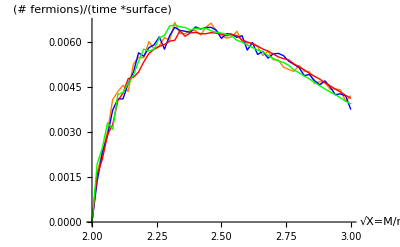

```mathematica
mcplot[2,2,{2,2,2,2,2},1,.1]
```

#### Plots. y=1, cosmin=0

```mathematica
y=1;cosmin=0;
```

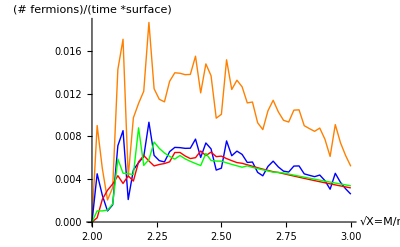

```mathematica
mcplot[1,1,{1,1,1,1,1}]
```

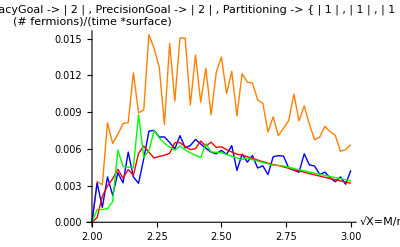

```mathematica
mcplot[2,2,{1,1,1,1,1}]
```

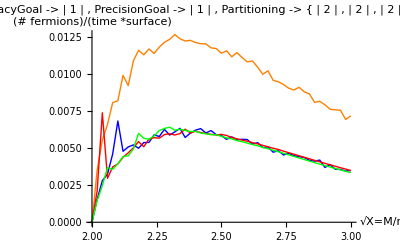

```mathematica
mcplot[1,1,{2,2,2,2,2}]
```

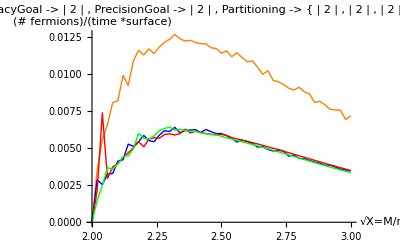

```mathematica
mcplot[2,2,{2,2,2,2,2}]
```

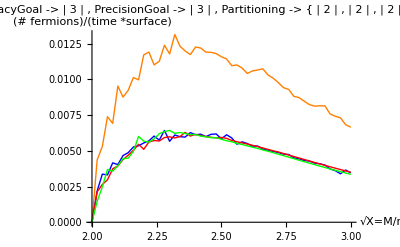

```mathematica
mcplot[3,3,{2,2,2,2,2}]
```

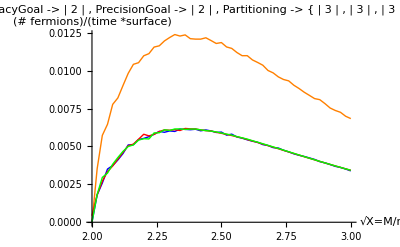

```mathematica
mcplot[2,2,{3,3,3,3,3}]
```

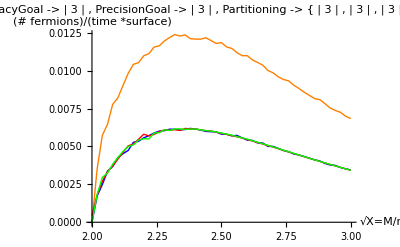

```mathematica
mcplot[3,3,{3,3,3,3,3}]
```

#### Plots. y = 1, cosmin = .8

```mathematica
y=1;cosmin=.8;
```

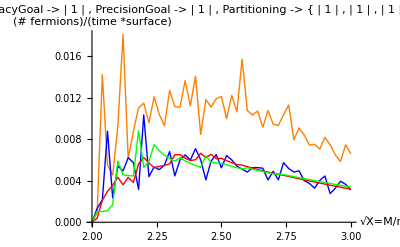

```mathematica
mcplot[1,1,{1,1,1,1,1}]
```

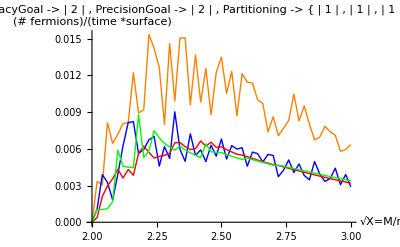

```mathematica
mcplot[2,2,{1,1,1,1,1}]
```

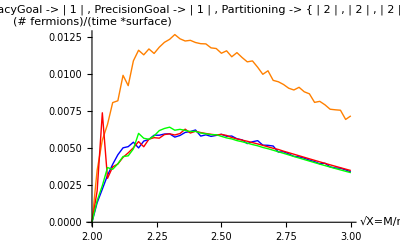

```mathematica
mcplot[1,1,{2,2,2,2,2}]
```

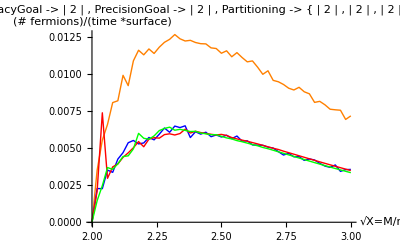

```mathematica
mcplot[2,2,{2,2,2,2,2}]
```

### Stuetzstellen

```mathematica
Graphics[
{PointSize[.01],Point[Reap[NIntegrate[f[x]*f[y],{x,0,2},{y,0,2},EvaluationMonitor:>Sow[{x}]]][[2,1]]]},Axes->True,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
f[x_]:=x^3;
```

```mathematica
mclist=Reap[Print@NIntegrate[f[x]*f[y],{x,0,2},{y,0,2},MaxPoints->50000,EvaluationMonitor:>Sow[{x,y}],Method->"QuasiMonteCarlo"]];Length[mclist[[2,1]]]
```

15.9998

50000

```mathematica
StepMonitor:>Print[x]
```

```mathematica
Block[{a,b},Graphics@{Point[Block[{n=1},{a,b}=Reap[NIntegrate[f[x],{x,0,1},Method->"MonteCarlo",EvaluationMonitor:>{Sow[{n,x}];n=n+1;}]]][[2,1]]]};a]
```

1.25267

```mathematica
{x,x,x}/.x-> RandomReal[]
```

{0.596283,0.596283,0.596283}

```mathematica
8
```

### Single fermion spectrum

Differential (w.r.t to x) probality  density of evaporation of a single lepton with x=p/m, where 0 < x < s^(1/2)/2m:

```mathematica
p[x_]:=m^2/(2 π^2)1/Sqrt[1+x^2] x^3/Exp[11.24/(2π)y Sqrt[1+x^2]]/.{m->1,y->1/2};p[x]
```

(ⅇ^(-0.894451 √(1+x^2)) x^3)/(2 π^2 √(1+x^2))

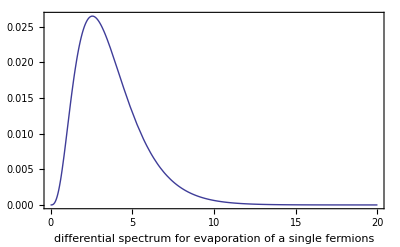

```mathematica
Plot[p[x],{x,0,20},Frame->True,FrameLabel->"differential spectrum for evaporation of a single fermions"]
```

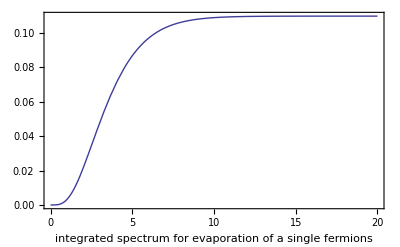

```mathematica
Plot[NIntegrate[p[x],{x,0,xmax}],{xmax,0,20},AxesLabel->{"Probality","x"},Frame->True,FrameLabel->"integrated spectrum for evaporation of a single fermions"]
```

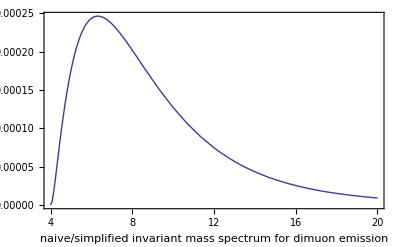

```mathematica
Plot[NIntegrate[solx1poscon*p[x2]p[solx1],{x2,0,20},{cos,0.8,0.99}],{X,4,20},PerformanceGoal->"Speed",Frame->True,FrameLabel->"naive/simplified invariant mass spectrum for dimuon emission"]
```